## Hairy black hole in cubic Horndeski theory

See [Bernardo, R. C., & Vega, I. (2019). Hair-dressing Horndeski: An approach for obtaining hairy solutions in cubic Horndeski gravity. Physical Review D, 99(12), 124049] which we refer to as Ref. [1].

*During the work for Ref. [1], I have not yet started using Mathematica. Instead, all the work done has been calculated by hand (very inefficient) and the figures and numerical results have been obtained using python.

Author: Reggie Bernardo

### Derivation of hairy black hole

We derive the hairy black hole solution presented in Ref. [1].

#### Starting point: Eq. (75)

```mathematica
eq75=-12 f[r]^2-(-4+r^2 R[r]+3 r f'[r]) (-4+r^2 R[r]+4 r f'[r])+2 f[r] (14+r (-6 f'[r]+r (-2 R[r]+r R'[r]+3 f''[r])))==0;
```

#### Step 1: Specify ansatz that decouples the metric functions R and f.

```mathematica
$Assumptions=r≥√Q;
f[r_]=1-(Q/(r^2));
solR=(DSolve[eq75//Simplify,R,r][[1]]);

Rs[r_]=(R[r]/.solR//Simplify);

"f(r)"==f[r]
"R[r]"==Rs[r]
```

f(r)==1-Q/r^2

R[r]==-(2 (r √(-Q+r^2)+Q C[1]+Q Log[r+√(-Q+r^2)]))/(r^4 (C[1]+Log[r+√(-Q+r^2)]))

Compute the metric function h(r) from Eq. (74).

```mathematica
eq74=h'[r]/h[r]==-(4/r)+(4/(r*f[r]))-(3*f'[r]/f[r])-(r*R[r]/f[r]);
hsol=DSolve[eq74/.R->Function[r,Rs[r]]//Simplify,h,r][[1]];

hs[r_]=(h[r]/.hsol//Simplify);

"h(r)"==hs[r]
```

h(r)==C[2] (C[1]+Log[r+√(-Q+r^2)])^2

Check if Eq. (24) is satisfied.

```mathematica
eq24=-(4/(r^3))-2*(f[r]*h''[r]/(r*h[r]))+(f[r]*(h'[r]^2)/(r*(h[r]^2)))-2*f[r]*h'[r]/(h[r]*(r^2))+(4*f[r]/(r^3))-(f'[r]*h'[r]/(h[r]*r))+(2*f'[r]/(r^2))==0;

eq24/.{h->Function[r,hs[r]],R->Function[r,Rs[r]]}//Simplify
```

True

The result has to be “True” for consistency.

#### Step 2: Compute the kinetic density.

```mathematica
X[r_]=-L-(2/(r^2))+(2*f[r]*h'[r]/(r*h[r]))+(2*f[r]/(r^2))/.h->Function[r,hs[r]]//Simplify;

"X[r]"==Series[X[r],{r,Infinity, 3}]
```

X[r]==-L+4/((C[1]+Log[2]-Log[1/r]) r^2)+O[1/r]^4

Scalar field follows from the kinetic density.

```mathematica
ϕ[r_]=Sqrt[-2*X[r]/f[r]]//Simplify;

"ϕ(r)"==Series[ϕ[r],{r,Infinity,3}]
```

ϕ(r)==√2 √L+((√L Q)/(√2)-(2 √2)/(√L (C[1]+Log[2]-Log[1/r])))/r^2+O[1/r]^4

#### Step 3: Compute Horndeski theory

The model function could be obtained numerically using Eq. (28).

```mathematica
eq28=GX √(-X[r])√(f[r]/2)(hs'[r]/hs[r]+4/r)==1;
solGX=Solve[eq28//Simplify,GX][[1]];

"G_X(X(r))"==(GX/.solGX//Simplify)
```

G_X(X(r))==(√2)/((4/r+2/(√(-Q+r^2) (C[1]+Log[r+√(-Q+r^2)]))) √((1-Q/r^2) (L+(2 (Q-(2 r √(-Q+r^2))/(C[1]+Log[r+√(-Q+r^2)])))/r^4)))

#### Summary

We have derived a larger class of solution than just a black hole. To zero in on the black hole requires making h and f vanish at the same event horizon r=√Q. It is easy to show that this is tantamount to the rule...

```mathematica
ruleBH={C[1]->-Log[√Q],C[2]->b};
```

The black hole solution is therefore...

```mathematica
fBH[r_]=f[r];
hBH[r_]=(hs[r]/.ruleBH//Simplify);
RBH[r_]=(Rs[r]/.ruleBH//Simplify);
XBH[r_]=(X[r]/.ruleBH//Simplify);

"f(r)"==fBH[r]
"h(r)"==hBH[r]
"R(r)"==RBH[r]
"X(r)"==XBH[r]
```

f(r)==1-Q/r^2

h(r)==b Log[(√Q)/(r+√(-Q+r^2))]^2

R(r)==(2 r √(-Q+r^2)-Q Log[Q]+2 Q Log[r+√(-Q+r^2)])/(r^4 Log[(√Q)/(r+√(-Q+r^2))])

X(r)==-L-(2 Q)/r^4+(4 √(-Q+r^2))/(r^3 Log[(r+√(-Q+r^2))/(√Q)])

These are Eqs. (89), (90), (92), and (93) in Ref. [1], after a bit of massaging.

### Some properties

Here are some of the properties of the hairy black hole derived above.

```mathematica
Geodesic potential
```

Geodesic potential

Here is the geodesic potential for test objects in the spacetime.

```mathematica
V[r_]=fBH[r]*(1+((l^2)/(r^2)))-(fBH[r]/hBH[r])//Simplify;

"V(r)"==Series[V[r],{r,Infinity,3}]
```

V(r)==(1-1/(b (Log[(√Q)/2]+Log[1/r])^2))+(l^2-Q+Q/(2 b (Log[(√Q)/2]+Log[1/r])^3)+Q/(b (Log[(√Q)/2]+Log[1/r])^2))/r^2+O[1/r]^4

A plot of which is shown below for two cases.

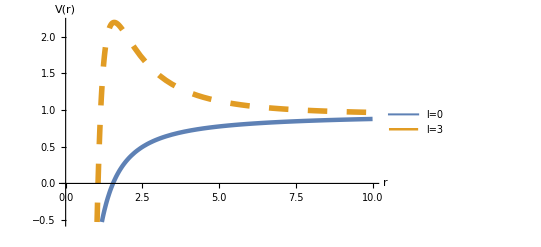

```mathematica
param={Q->1,L->2,b->1};
Plot[{V[r]/.param/.l->0,V[r]/.param/.l->3},{r,0,10},AxesLabel->{"r","V(r)"},AxesStyle->Directive[Black,15],LabelStyle->Directive[Black,Bold],Ticks->Automatic,TicksStyle->Directive[Black,15],PlotLegends->{"l=0","l=3"},PlotStyle->{Thickness[0.008],{Dashing[Large],Thickness[0.01]}}]
Clear[Q,l]
```

Here is a plot of the metric functions, the kinetic density, and the Ricci scalar.

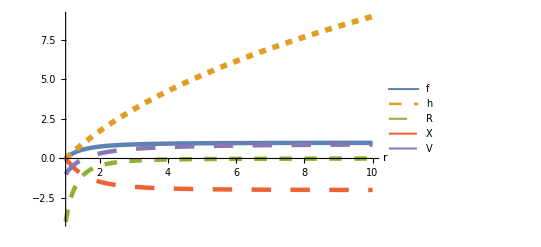

```mathematica
Plot[{fBH[r]/.param,hBH[r]/.param,RBH[r]/.param,XBH[r]/.param,V[r]/.param/.l->0},{r,1,10},AxesLabel->{r,},AxesStyle->Directive[Black,15],LabelStyle->Directive[Black,Bold],Ticks->Automatic,TicksStyle->Directive[Black,15],PlotLegends->{"f","h","R","X","V"},PlotStyle->{Thickness[0.008],{Dashing[Small],Thickness[0.01]},{Dashing[Medium],Thickness[0.008]},{Dashing[Large],Thickness[0.008]},{Dashing[Large],Thickness[0.008]}}]
```

Both f and h vanish at the same place, R vanishes asymptotically (spacetime is asymptotically Ricci flat), X becomes constant far away from the hole.

### Proper time to enter horizon

Here is the proper time for an object to the horizon r/√Q=1 starting at r/√Q=10.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {8.48842}. NIntegrate obtained -15.2788+8.82201 ⅈ and 0.246979 for the integral and error estimates.

Plot::exclul: {√(-(1-Q Power[«2»]) (1+Power[«2»] Power[«2»]-Power[«2»] Power[«2»])+((1-Q «1») y)/(b («1»)^2))-0} must be a list of equalities or real-valued functions.

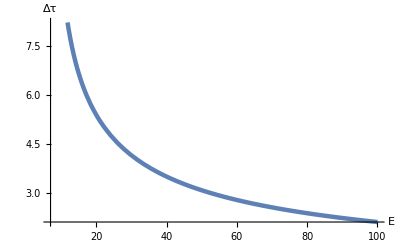

```mathematica
Propertime[y_]:=-NIntegrate[1/Sqrt[(fBH[r]/hBH[r])*y-V[r]]/.param/.l->0,{r,10,1}]

Plot[Propertime[y],{y,7,100},AxesLabel->{"E","Δτ"},AxesStyle->Directive[Black,15],LabelStyle->Directive[Black,Bold],Ticks->Automatic,TicksStyle->Directive[Black,15],PlotStyle->{Thickness[0.008]}]
```